# one leg model

```mathematica
ClearAll["Global`*"]
ClearAll[Derivative]
```

```mathematica
fx=x[t] ω^2 (l/(√(x[t]^2+y[t]^2))-1)
fy=y[t] ω^2(l/(√(x[t]^2+y[t]^2))-1)-g
```

ω^2 x[t] (-1+l/(√(x[t]^2+y[t]^2)))

-g+ω^2 y[t] (-1+l/(√(x[t]^2+y[t]^2)))

```mathematica
Params={ω->0.1,g->10,l->1};
f1nx=fx/.Params/.{x[t]->xn[i],y[t]->yn[i]};
f1ny=fy/.Params/.{x[t]->xn[i],y[t]->yn[i]};
xn'[0]=1;
yn'[0]=-0.5;
xn[0]=-1;
yn[0]=1;
Nmax=500;
Δt=0.005;


For[i=0,i<=Nmax,i++,
If[Mod[i,IntegerPart[0.25Nmax]]==0,Print[N[i/Nmax 100]]];

K1vx=f1nx/.{xn[i]->xn[i],yn[i]->yn[i]};
K2vx=f1nx/.{xn[i]->xn[i]+0.5 K1vx,yn[i]->yn[i]+0.5K1vx};
K3vx=f1nx/.{xn[i]->xn[i]+0.5 K2vx,yn[i]->yn[i]+0.5K2vx};
K4vx=f1nx/.{xn[i]->xn[i]+ K3vx,yn[i]->yn[i]+K3vx};
xn'[i+1]=xn'[i]+Δt/6(K1vx+2K2vx+2K3vx+K4vx);

K1x=xn'[i];
K2x=xn'[i]+0.5K1x;
K3x=xn'[i]+0.5 K2x;
K4x=xn'[i]+K3x;

xn[i+1]=xn[i]+Δt/6(K1x+2K2x+2K3x+K4x);

K1vy=f1ny;
K2vy=f1ny/.{xn[i]->xn[i]+0.5 K1vy,yn[i]->yn[i]+0.5K1vy};
K3vy=f1ny/.{xn[i]->xn[i]+0.5 K2vy,yn[i]->yn[i]+0.5K2vy};
K4vy=f1ny/.{xn[i]->xn[i]+ K3vy,yn[i]->yn[i]+K3vy};
yn'[i+1]=yn'[i]+Δt/6(K1vy+2K2vy+2K3vy+K4vy);
K1y=yn'[i];
K2y=yn'[i]+0.5K1y;
K3y=yn'[i]+0.5 K2y;
K4y=yn'[i]+K3y;

yn[i+1]=yn[i]+Δt/6(K1y+2K2y+2K3y+K4y);
]
```

0.

25.

50.

75.

100.

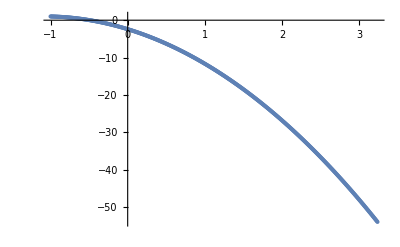

```mathematica
ListPlot[Table[{xn[n],yn[n]},{n,0,Nmax}],PlotRange->All]
```